```mathematica
Vector beam linear focusing simulation
```

```mathematica
Define parameters:
```

```mathematica
p=10;(*number of integration points*)
λ=1;(*wavelength*)
k=(2 π)/λ;(*wavenumber*)
NA=1.32;(*numerical aperture*)
n=1.518;(*refractive index*)
α=ArcSin[NA/n](*angular extent of aperture*)
min=-2 λ;max=2 λ;step = 100;(*transverse dimensions*)
zmin=-2 λ;zmax=2 λ;zstep=100;(*longitudinal dimensions*)
f=100000 λ;(*focal length*)
l0=1;(*peak field amplitude*)
A=(π f l0)/λ;(*constant before integration*)
β=1.5;(*ratio of pupil radius to beam waist AT ENTRANCE PUPIL*)
u[z_]:=k z Sin[α]^2;(*as defined in Richards & Wolf*)
v2d = Table[{k Sin[α] √(x^2+y^2),z},{x,Range[min,max,(max-min)/step]},{y,Range[min,max,(max-min)/step]},{z,Range[zmin,zmax,(zmax-zmin)/zstep]}];(*array with {v,z} value of each physical position*)
ϕ=Table[Arg[Complex[y,x]],{x,Range[min,max,(max-min)/step]},{y,Range[min,max,(max-min)/step]}];(*phase*)
apod[θ_]:=Exp[-β^2 (Sin[θ]/Sin[α])^2]BesselJ[1,2 β Sin[θ]/Sin[α]];(*apodization function*)
```

1.05432

```mathematica
Trapezoidal rule
```

```mathematica
I02d=I12d=I22d=0*v2d;
I02d[[All,All,All,2]]=I12d[[All,All,All,2]]=I22d[[All,All,All,2]]=v2d[[All,All,All,2]];
For[i=1,i<n,i++,I02d[[All,All,All,1]]=I02d[[All,All,All,1]]+(√Cos[i α/p]*apod[i α/p]*Sin[i α/p]*(1+Cos[i α/p])*BesselJ[0,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]]*Exp[I u[I02d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2]);
I12d[[All,All,All,1]]=I12d[[All,All,All,1]]+(√Cos[i α/p]*apod[i α/p]*Sin[i α/p]^2*BesselJ[1,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]]*Exp[I u[I12d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2]);
I22d[[All,All,All,1]]=I22d[[All,All,All,1]]+(√Cos[i α/p]*apod[i α/p]*Sin[i α/p]*(1-Cos[i α/p])*BesselJ[2,v2d[[All,All,All,1]] Sin[i α/p]/Sin[α]]* Exp[I u[I22d[[All,All,All,2]]] Cos[i α/p]/Sin[α]^2])];

I02d[[All,All,All,1]]=α/p(I02d[[All,All,All,1]]+(1/2 √Cos[α]*apod[α]*Sin[α]*(1+Cos[α])*BesselJ[0,v2d[[All,All,All,1]]]*Exp[I u[I02d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));
I12d[[All,All,All,1]]=α/p(I12d[[All,All,All,1]]+(1/2 √Cos[α]*apod[α]*Sin[α]^2*BesselJ[1,v2d[[All,All,All,1]]]*Exp[I u[I12d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));
I22d[[All,All,All,1]]=α/p(I22d[[All,All,All,1]]+(1/2 √Cos[α]*apod[α]*Sin[α]*(1-Cos[α])*BesselJ[2,v2d[[All,All,All,1]]]*Exp[I u[I22d[[All,All,All,2]]] Cos[α]/Sin[α]^2]));

Ex2d=Ey2d=Ez2d=0*v2d;
Ex2d[[All,All,All,2]]=Ey2d[[All,All,All,2]]=Ez2d[[All,All,All,2]]=v2d[[All,All,All,2]];
Ex2d[[All,All,All,1]]=-I A (I02d[[All,All,All,1]]+I22d[[All,All,All,1]] Cos[2 ϕ]);
Ey2d[[All,All,All,1]]=-I A (I22d[[All,All,All,1]] Sin[2 ϕ]);
Ez2d[[All,All,All,1]]=-2 I A (I12d[[All,All,All,1]] Cos[ϕ]);
```

```mathematica
Plots
```

```mathematica
X component intensity (for chosen z position)
```

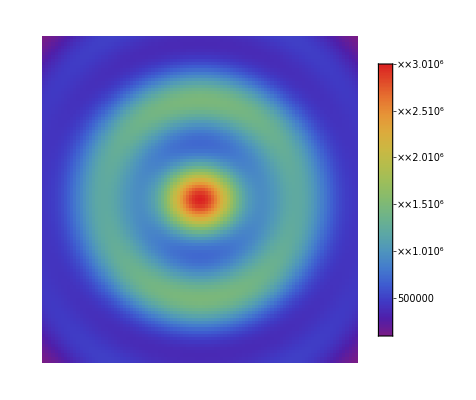

```mathematica
ArrayPlot[Abs[Ex2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Y component intensity (for chosen z position)
```

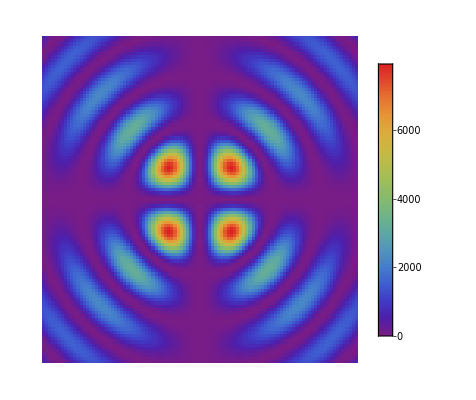

```mathematica
ArrayPlot[Abs[Ey2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Z component intensity (for chosen z position)
```

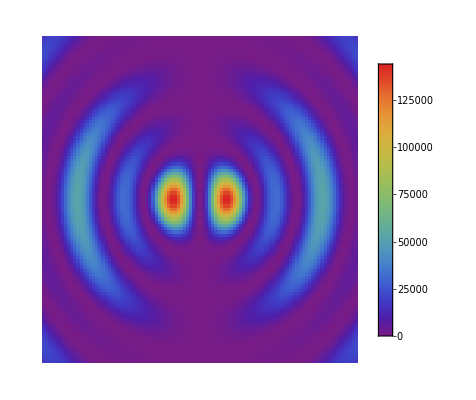

```mathematica
ArrayPlot[Abs[Ez2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```